```mathematica
g[y_]=D[rbar((1+y)/(1-y))^(1/α),y];
F[y_]=Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2];
```

80.812

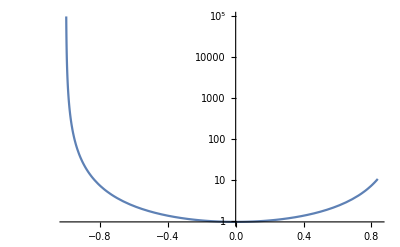

(0.500776 0.000775601^(-1+1/α) rbar)/α

```mathematica
rbar=3;α=4;
g[-0.99845]
LogPlot[F[y],{y,-0.99845,0.83735},PlotRange->All]
Clear[rbar,α]
```

```mathematica
(* This is the mapping with Surkus variable, as discussed in the paper *)
g[y_]=D[rbar((1+y)/(1-y))^(1/α),y];

(* g[y] for exponential mapping *)
g[y_]=1/(1+y α);

(* g[y] for quadratic mapping *)
(* g[y_]=1/(√(1+2 y α));*)

(* This choice uses inverse coordinate, and makes the additional term null *)
(* g[y_]=b(-a/y-(1-a y)/y^2);*)

Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2,{y>0,α>0}]
```

α^2/(4 (1+y α)^2)

```mathematica
D[1/y,y]
```

-1/y^2

```mathematica
Clear[g]
g[y_]=a/(y+b)^2;
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2
```

0

```mathematica
DSolve[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2==0,g[y],y]
```

{{g[y]→C[2]/(y+2 C[1])^2}}

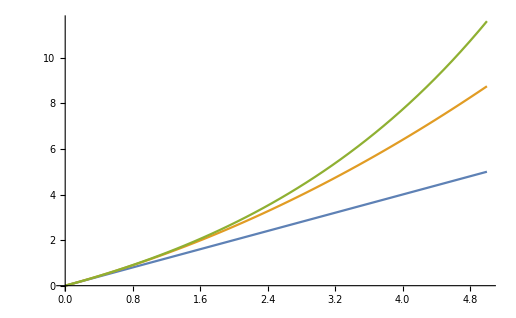

```mathematica
α=0.3;
Plot[{r,r+α/2 r^2,(ⅇ^(α r)-1)/α},{r,0,5}]
Clear[α]
```

```mathematica
(* g[y] for exponential mapping *)
1/(1+y α);

(* g[y] for quadratic mapping *)
1/(√(1+2 y α));
```

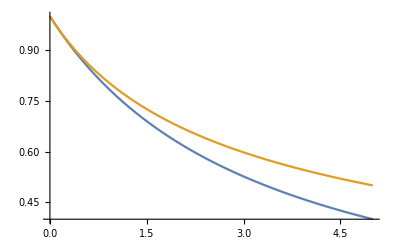

```mathematica
α=0.3;
Plot[{1/(1+y α),1/(√(1+2 y α))},{y,0,5}]
Clear[α]
```

```mathematica
Series[(f[x+h]-2f[x]+f[x-h])/h^2,{h,0,2}]
```

f''[x]+1/12 f^(4)[x] h^2+O[h]^3

```mathematica
f[x+h]==f[x](2-q[x] h^2)-f[x-h]
```

```mathematica
(f[x+h]-2f[x]+f[x-h])/h^2==-q[x]f[x]
```

```mathematica
Solve[y==r+(r/re)^2,r]//Simplify
```

{{r→-1/2 re (re+√(re^2+4 y))},{r→1/2 re (-re+√(re^2+4 y))}}

```mathematica
D[(-1+ⅇ^(y/rRef)) rRef,y]
```

ⅇ^(y/rRef)

```mathematica
g[y_]=ⅇ^(y/rRef);
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2//Simplify
Clear[g]
```

-1/(4 rRef^2)

```mathematica
Series[re/α((1+r/re)^α-1),{α,0,2}]
```

re Log[1+r/re]+1/2 re Log[1+r/re]^2 α+1/6 re Log[1+r/re]^3 α^2+O[α]^3

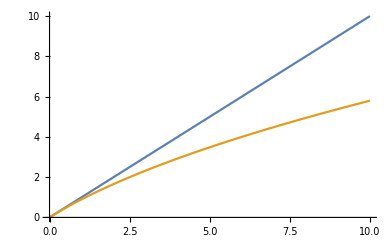

```mathematica
re=2;
Plot[{r,2re(√(1+r/re)-1)},{r,0,10}]
Clear[re]
```

```mathematica
Solve[y==2re(√(1+r/re)-1),r]
g[y_]=D[(4 re y+y^2)/(4 re),y]
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2//Simplify
Clear[g]
```

{{r→(4 re y+y^2)/(4 re)}}

(4 re+2 y)/(4 re)

-3/(4 (2 re+y)^2)

```mathematica
Simplify[Solve[y==rRef Log[1+r/rRef],r],{y>0,r>0,rRef>0}]
```

{{r→(-1+ⅇ^(y/rRef)) rRef}}

```mathematica
Clear[U,Q]
```

```mathematica
r[y_]= y^(1/6);
U=Cn/r[y]^6;
Q=2μ(energy-U);
g[y_]=r'[y];
g[y]^2 Q+(g''[y]/(2g[y])-3/4(g'[y]/g[y])^2)//Expand
Normal[Series[%,{y,∞,0}]];
```

35/(144 y^2)-(Cn μ)/(18 y^(8/3))+(energy μ)/(18 y^(5/3))